### 1. Checking Depth of the Potential (Numerically)

First define the potential as follows (with gauge choice in place):

```mathematica
V=(m^2 ϕ^2)/2+(-1/3-a^2 m^2) ϕ^3+(a^2+(23 a^4 m^2)/6+(112 a^6 m^4)/9+(400 a^8 m^6)/9+(5056 a^10 m^8)/45+(30848 a^12 m^10)/135+(372224 a^14 m^12)/945+(111872 a^16 m^14)/189+(959488 a^18 m^16)/1215+(40306688 a^20 m^18)/42525+(483713024 a^22 m^20)/467775) ϕ^4+(-(13 a^4)/3-(370 a^6 m^2)/9-(2356 a^8 m^4)/9) ϕ^5+((97 a^6)/3+(7444 a^8 m^2)/15+(40016 a^10 m^4)/27+(16951588 a^12 m^6)/2025+(365040328 a^14 m^8)/4725+(704360354 a^16 m^10)/1575+(53044107164 a^18 m^12)/25515+(5345363837636 a^20 m^14)/637875+(212689374482008 a^22 m^16)/7016625) ϕ^6+(-(13532 a^8)/45-(1645424 a^10 m^2)/405-(246594764 a^12 m^4)/6075-(18403444376 a^14 m^6)/42525) ϕ^7+((1057238 a^10)/405+(528895198 a^12 m^2)/8505+(293278365536 a^14 m^4)/297675+(330220197478 a^16 m^6)/297675+(4539699316064 a^18 m^8)/535815+(3762791962092662 a^20 m^10)/13395375+(18508000088422676 a^22 m^12)/5893965) ϕ^8+(-(17612426 a^12)/567-(1376189404 a^14 m^2)/1323-(1461162201244 a^16 m^4)/178605-(152243548796524 a^18 m^6)/1607445-(14516307774038468 a^20 m^8)/8037225) ϕ^9+((17745598574 a^14)/42525+(91967935202338 a^16 m^2)/8037225+(3255947000654108 a^18 m^4)/14467005+(339406560100146388 a^20 m^6)/72335025-(36650456262120146896 a^22 m^8)/3978426375) ϕ^10+(-(5599006958392 a^16)/1148175-(2226671149812904 a^18 m^2)/10333575-(461350316377218328 a^20 m^4)/72335025-(13262953310597307088 a^22 m^6)/795685275) ϕ^11+((604370472837748 a^18)/8037225+(3570960644823919238 a^20 m^2)/795685275+(107753866659559323248 a^22 m^4)/1705039875) ϕ^12+(-(1954323884798776 a^20)/1515591-(60074374172932678156 a^22 m^2)/1023023925) ϕ^13+(11898606015180066008 a^22 ϕ^14)/651015225;
```

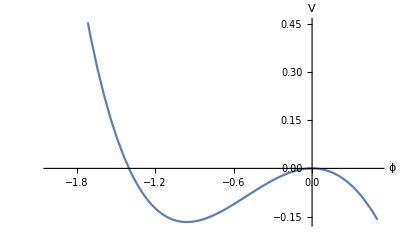

```mathematica
Pot[ϕ_,r_]:=V/.{m-> I, a-> r}//Evaluate
Plot[Pot[ϕ,0.2],{ϕ,-2,.5},AxesLabel->{"ϕ","V"}]
```

Our quest is to find the depth of the potential as more orders of r included. We can do this numerically as follows (I will always most order available in the code)

```mathematica
r0=0.2;
Table[FindMinimum[(Series[Pot[ϕ,r],{r,0,i}]//Normal)/.{r->r0},{ϕ,-1}],{i,0,22,2}]//Quiet//TableForm
```

-0.166667 | ϕ→-1.
-0.167328 | ϕ→-0.966517
-0.16686 | ϕ→-0.959744
-0.166711 | ϕ→-0.958271
-0.166678 | ϕ→-0.957906
-0.166669 | ϕ→-0.957817
-0.166667 | ϕ→-0.957789
-0.166667 | ϕ→-0.95778
-0.166667 | ϕ→-0.957777
-0.166667 | ϕ→-0.957776
-0.166667 | ϕ→-0.957775
-0.166667 | ϕ→-0.957775

It seems depth is converging back to its original value -1/6 after enough field redefinitions!

### 2. Checking Depth of the Potential (Analytically)

Now try to check it analytically. To do that we need to solve for extremum analytically, which we can do with the following perturbative ansatz and the position of critical point (working to the order r^22 always):

```mathematica
ClearAll[B]
ϕA=Sum[B[i]r^i,{i,0,22,2}];
coeff=CoefficientList[Series[D[Pot[ϕ,r],ϕ]/.{ϕ->ϕA},{r,0,22}]//Normal,r];
For[i=0,i≤22,i=i+2,
Set@@@(Solve[coeff[[i+1]]==0,B[i]]//First);
]
ϕA
ϕA/.{r->r0}
```

-1+r^2+(4 r^4)/3+(11 r^6)/9+(362 r^8)/45-(41326 r^10)/405+(27957988 r^12)/42525-(204508243 r^14)/297675+(1108413786946 r^16)/8037225-(8452860382558 r^18)/10333575+(19774453755325648 r^20)/3978426375-(11164201926589795042 r^22)/35805837375

-0.957775

When inserted into the potential it exactly gives -1/6:

```mathematica
Series[Pot[ϕA,r],{r,0,23}]
```

-1/6+O[r]^24

Discrepancy between numerical values for low orders in r is probably because of numerics and not systematically implementing expansions. This would be the right result!

As a consistency check, let’s evaluate V(ϕ=-1)

```mathematica
Pot[-1,r]
```

-1/6+r^4/2+(11 r^6)/3+(196 r^8)/9+(19186 r^10)/135+(351608 r^12)/405+(306517178 r^14)/42525+(17124406934 r^16)/297675+(4967565430336 r^18)/8037225+(1534899906921544 r^20)/361675125+(495306912669469256 r^22)/11935279125

As expected from the first order perturbation theory , leading term (r^2) vanishes.

### 3. Checking Depth of the Gauge-unfixed Potential

We can also try to implement ideas that we have in method 2, without fixing the gauge. Remember Potential in this case is given by (From Harold’s Code, now to the r^10)

```mathematica
ClearAll[c]
VTD=-(-1/2 m^2 ϕ[t]^2+(1/3+a^2 m^2+a^4 m^4 (3/2-3/2 c[1,3,0])+a^6 m^6 (2-3/2 c[1,3,2])+a^8 m^8 (9/4-3/2 c[1,3,4])+a^10 m^10 (23/10-3/2 c[1,3,6]-3 c[3,3,0])) ϕ[t]^3+(-a^2+a^4 m^2 (-19/3+5/2 c[1,3,0])+a^6 m^4 (-419/18+15/2 c[1,3,0]+5/2 c[1,3,2])+a^8 m^6 (-4595/72+45/4 c[1,3,0]-45/8 c[1,3,0]^2+15/2 c[1,3,2]+5/2 c[1,3,4])+a^10 m^8 (-25639/180+15 c[1,3,0]+45/4 c[1,3,2]-45/4 c[1,3,0] c[1,3,2]+15/2 c[1,3,4]+5/2 c[1,3,6]+5 c[3,3,0])) ϕ[t]^4+(a^4 (16/3-c[1,3,0])+a^6 m^2 (517/9-15 c[1,3,0]-c[1,3,2])+a^8 m^4 (12331/36-75 c[1,3,0]+63/4 c[1,3,0]^2-15 c[1,3,2]-c[1,3,4])+a^10 m^6 (108739/72-301 c[1,3,0]+243/8 c[1,3,0]^2-75 c[1,3,2]+63/2 c[1,3,0] c[1,3,2]-15 c[1,3,4]-c[1,3,6]-15/8 c[1,5,0]-2 c[3,3,0])) ϕ[t]^5+(a^6 (-118/3+7 c[1,3,0])+a^8 m^2 (-9194/15+364/3 c[1,3,0]-14 c[1,3,0]^2+7 c[1,3,2])+a^10 m^4 (-5684671/1080+9478/9 c[1,3,0]-861/8 c[1,3,0]^2+364/3 c[1,3,2]-28 c[1,3,0] c[1,3,2]+7 c[1,3,4]+35/8 c[1,5,0])) ϕ[t]^6+(a^8 (15812/45-164/3 c[1,3,0]+4 c[1,3,0]^2)+a^10 m^2 (199094/27-11744/9 c[1,3,0]+114 c[1,3,0]^2-164/3 c[1,3,2]+8 c[1,3,0] c[1,3,2]-10/3 c[1,5,0])) ϕ[t]^7+a^10 (-324791/90+1564/3 c[1,3,0]-75/2 c[1,3,0]^2+5/6 c[1,5,0]) ϕ[t]^8);
PotTD[ϕ_,r_]:=VTD/.{ϕ[t]->ϕ, m-> I, a-> r}//Evaluate
```

Again putting the ansatz in, we find:

```mathematica
ClearAll[B]
ϕA=Sum[B[i]r^i,{i,0,10,2}];
coeff=CoefficientList[Series[D[PotTD[ϕ,r],ϕ]/.{ϕ->ϕA},{r,0,10}]//Normal,r];
For[i=0,i≤10,i=i+2,
Set@@@(Solve[coeff[[i+1]]==0,B[i]]//First);
]
ϕA
```

-1+r^2+1/6 r^4 (5+3 c[1,3,0])+1/18 r^6 (34-9 c[1,3,2])+1/180 r^8 (1313+90 c[1,3,4])+1/120 r^10 (4207-700 c[1,3,0]-225 c[1,3,0]^2-60 c[1,3,6]-25 c[1,5,0]-120 c[3,3,0])

This gives

```mathematica
Series[PotTD[ϕA,r],{r,0,11}]//FullSimplify
```

-1/6+O[r]^12

Again, there is no change in the depth of the well. This is reassuring check that total derivatives don’t effect the final observables!

As a consistency check, let’s evaluate V(ϕ=-1)

```mathematica
Collect[PotTD[-1,r],r]
```

-1/6+r^4/2+r^6 (19/6+1/2 c[1,3,0])+r^8 (1397/72+35/12 c[1,3,0]+1/8 c[1,3,0]^2-1/2 c[1,3,2])+r^10 (34667/270+148/9 c[1,3,0]+3/4 c[1,3,0]^2-35/12 c[1,3,2]-1/4 c[1,3,0] c[1,3,2]+1/2 c[1,3,4])

As expected from the first order perturbation theory , leading term (r^2) vanishes.

### 4. A New Gauge

There is a gauge choice we can make so that the vacuum is fixed at -1+r^2:

```mathematica
choice={c[1,3,0]-> -5/3, c[1,3,2]-> 34/9, c[1,3,4]->- 1313/90,c[1,3,6]->14246/180 ,c[1,5,0]-> 0, c[3,3,0]->0};
ϕA/.choice
```

-1+r^2

This makes potential equal to

-ϕ^2/2-(1/3-r^2+4 r^4+(11 r^6)/3+(362 r^8)/15+(1397 r^10)/12) ϕ^3-(-r^2+(21 r^4)/2-(79 r^6)/3+(319 r^8)/3+(6181 r^10)/180) ϕ^4-(7 r^4-(236 r^6)/3+(2346 r^8)/5-(315779 r^10)/180) ϕ^5-(-51 r^6+(4138 r^8)/5-(407111 r^10)/60) ϕ^6-((2268 r^8)/5-(86476 r^10)/9) ϕ^7+(206183 r^10 ϕ^8)/45

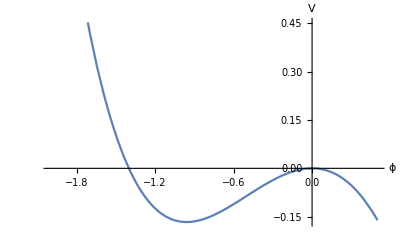

```mathematica
PotTD[ϕ,r]/.choice
Plot[PotTD[ϕ,r]/.choice/.{r->r0},{ϕ,-2,0.5}, AxesLabel->{"ϕ","V"}]
```

And the depth is still at -1/6:

```mathematica
Series[PotTD[ϕA/.choice,r]/.choice,{r,0,11}]//FullSimplify
```

-1/6+O[r]^12

It might be useful to investigate what happens as r->1, since two vacua become one!

```mathematica
Collect[PotTD[ϕ,1]/.choice,ϕ]
```

-ϕ^2/2-(2951 ϕ^3)/20-(22291 ϕ^4)/180+(244223 ϕ^5)/180+(72103 ϕ^6)/12+(411968 ϕ^7)/45+(206183 ϕ^8)/45

### 5. Sum Rules

The results above motivates us to investigate sum rules. Let us consider the most general potential to the given order of r

```mathematica
order=10;
ClearAll[α];
sum1[e_]=Sum[α[e,i]ϕ^i,{i,3,3+e/2}];
VSR=-ϕ^2/2-ϕ^3/3+ Sum[r^e sum1[e],{e,2,order,2}]

PotSR[ϕ_,r_]:= VSR//Evaluate;
```

-ϕ^2/2-ϕ^3/3+r^2 (ϕ^3 α[2,3]+ϕ^4 α[2,4])+r^4 (ϕ^3 α[4,3]+ϕ^4 α[4,4]+ϕ^5 α[4,5])+r^6 (ϕ^3 α[6,3]+ϕ^4 α[6,4]+ϕ^5 α[6,5]+ϕ^6 α[6,6])+r^8 (ϕ^3 α[8,3]+ϕ^4 α[8,4]+ϕ^5 α[8,5]+ϕ^6 α[8,6]+ϕ^7 α[8,7])+r^10 (ϕ^3 α[10,3]+ϕ^4 α[10,4]+ϕ^5 α[10,5]+ϕ^6 α[10,6]+ϕ^7 α[10,7]+ϕ^8 α[10,8])

Here first index of α is power of r, and second one is power of ϕ. Repeating our steps to find the depth of the potential we get sum rules:

```mathematica
ClearAll[B]
ϕA=Sum[B[i]r^i,{i,0,order,2}];
coeff=CoefficientList[Series[D[PotSR[ϕ,r],ϕ]/.{ϕ->ϕA},{r,0,order}]//Normal,r];
For[i=0,i≤order,i=i+2,
Set@@@(Solve[coeff[[i+1]]==0,B[i]]//First);
]

sumrules=DeleteCases[CoefficientList[Series[PotSR[ϕA,r],{r,0,order+1}]//FullSimplify,r][[3;;]],0,Infinity];
sumrules//TableForm
```

-α[2,3]+α[2,4]
-1/2 (3 α[2,3]-4 α[2,4])^2-α[4,3]+α[4,4]-α[4,5]
-1/3 (3 α[2,3]-4 α[2,4]) (18 α[2,3]^2-66 α[2,3] α[2,4]+56 α[2,4]^2+9 α[4,3]-12 α[4,4]+15 α[4,5])-α[6,3]+α[6,4]-α[6,5]+α[6,6]
-135/2 α[2,3]^4+540 α[2,3]^3 α[2,4]-768 α[2,4]^4-1/2 (3 α[4,3]-4 α[4,4]+5 α[4,5])^2-9 α[2,3]^2 (168 α[2,4]^2+6 α[4,3]-10 α[4,4]+15 α[4,5])-16 α[2,4]^2 (9 α[4,3]-14 α[4,4]+20 α[4,5])+4 α[2,4] (3 α[6,3]-4 α[6,4]+5 α[6,5]-6 α[6,6])+α[2,3] (4 α[2,4] (448 α[2,4]^2+45 α[4,3]-72 α[4,4]+105 α[4,5])+3 (-3 α[6,3]+4 α[6,4]-5 α[6,5]+6 α[6,6]))-α[8,3]+α[8,4]-α[8,5]+α[8,6]-α[8,7]
-243 α[2,3]^5+2835 α[2,3]^4 α[2,4]+8448 α[2,4]^5+64 α[2,4]^3 (28 α[4,3]-48 α[4,4]+75 α[4,5])-27 α[2,3]^3 (448 α[2,4]^2+5 (2 α[4,3]-4 α[4,4]+7 α[4,5]))-16 α[2,4]^2 (9 α[6,3]-14 α[6,4]+20 α[6,5]-27 α[6,6])-(3 α[4,3]-4 α[4,4]+5 α[4,5]) (3 α[6,3]-4 α[6,4]+5 α[6,5]-6 α[6,6])+9 α[2,3]^2 (4 α[2,4] (672 α[2,4]^2+45 α[4,3]-84 α[4,4]+140 α[4,5])-6 α[6,3]+10 α[6,4]-15 α[6,5]+21 α[6,6])-3 α[2,3] (7680 α[2,4]^4+2 (3 α[4,3]-4 α[4,4]+5 α[4,5]) (3 α[4,3]-6 α[4,4]+10 α[4,5])+16 α[2,4]^2 (63 α[4,3]-112 α[4,4]+180 α[4,5])+4 α[2,4] (-15 α[6,3]+24 α[6,4]-35 α[6,5]+48 α[6,6])+3 α[8,3]-4 α[8,4]+5 α[8,5]-6 α[8,6]+7 α[8,7])+2 α[2,4] ((3 α[4,3]-4 α[4,4]+5 α[4,5]) (15 α[4,3]-28 α[4,4]+45 α[4,5])+2 (3 α[8,3]-4 α[8,4]+5 α[8,5]-6 α[8,6]+7 α[8,7]))-α[10,3]+α[10,4]-α[10,5]+α[10,6]-α[10,7]+α[10,8]

I don’t know what to make of this?

### 6. Covariant Potential (Old)

The covariant potential is (Harold’s result, only given to r^8):

```mathematica
V=-ϕ^2/2-1/3 ϕ^3+2(r^6-(50 r^8)/3) ϕ^4-4(-r^6+54 r^8) ϕ^5+2(r^6-167 r^8 ) ϕ^6-((454 r^8)/3) ϕ^7;
```

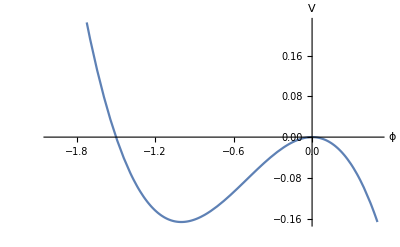

```mathematica
Pot[ϕ_,r_]:=V//Evaluate
Plot[Pot[ϕ,0.2],{ϕ,-2,0.5},AxesLabel->{"ϕ","V"}]
```

Our quest is to find the depth of the potential as more orders of r included. We can do this numerically as follows:

```mathematica
r0=0.2;
Table[FindMinimum[(Series[Pot[ϕ,r],{r,0,i}]//Normal)/.{r->r0},{ϕ,-1}],{i,0,8,2}]//Quiet//TableForm
```

-0.166667 | ϕ→-1.
-0.166667 | ϕ→-1.
-0.166667 | ϕ→-1.
-0.166667 | ϕ→-1.
-0.166667 | ϕ→-0.999995

It seems depth is converging back to its original value -1/6 too! Now try to check it analytically. To do that we need to solve for extremum analytically, which we can do with the following perturbative ansatz and the position of critical point:

```mathematica
ClearAll[B]
ϕA=Sum[B[i]r^i,{i,0,8,2}];
coeff=CoefficientList[Series[D[Pot[ϕ,r],ϕ]/.{ϕ->ϕA},{r,0,8}]//Normal,r];
For[i=0,i≤8,i=i+2,
Set@@@(Solve[coeff[[i+1]]==0,B[i]]//First);
]
ϕA
ϕA/.{r->r0}
```

-1+2 r^8

-0.999995

Note ϕA is corrected starting from r^8 ! When inserted into the potential it exactly gives -1/6:

```mathematica
Series[Pot[ϕA,r],{r,0,9}]
```

-1/6+O[r]^10

As a consistency check, let’s evaluate V(ϕ=-1)

```mathematica
Collect[Pot[-1,r],r]
```

-1/6

As expected from the first order perturbation theory , leading term (r^2) vanishes. In fact rest of the terms vanishes too! Unlike homogeneous case, we don’t have O(r^4) or higher corrections, because ϕA is corrected starting from r^8.

### 7. Covariant Potential (New)

The covariant potential is (Harold’s result, only given to r^8):

```mathematica
V=-ϕ^2/2-1/3 ϕ^3+(2 r^6-(110 r^8)/3) ϕ^4-(-4 r^6+(530 r^8)/3) ϕ^5+(2 r^6-(730 r^8)/3 ) ϕ^6-((310 r^8)/3) ϕ^7;
```

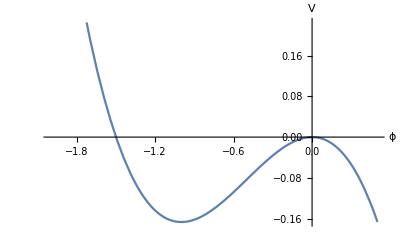

```mathematica
Pot[ϕ_,r_]:=V//Evaluate
Plot[Pot[ϕ,0.2],{ϕ,-2,0.5},AxesLabel->{"ϕ","V"}]
```

Our quest is to find the depth of the potential as more orders of r included. We can do this numerically as follows:

```mathematica
r0=0.2;
Table[FindMinimum[(Series[Pot[ϕ,r],{r,0,i}]//Normal)/.{r->r0},{ϕ,-1}],{i,0,8,2}]//Quiet//TableForm
```

-0.166667 | ϕ→-1.
-0.166667 | ϕ→-1.
-0.166667 | ϕ→-1.
-0.166667 | ϕ→-1.
-0.166667 | ϕ→-1.

It seems depth is not moving from its original value -1/6 too! Now try to check it analytically. To do that we need to solve for extremum analytically, which we can do with the following perturbative ansatz and the position of critical point:

```mathematica
ClearAll[B]
ϕA=Sum[B[i]r^i,{i,0,8,2}];
coeff=CoefficientList[Series[D[Pot[ϕ,r],ϕ]/.{ϕ->ϕA},{r,0,8}]//Normal,r];
For[i=0,i≤8,i=i+2,
Set@@@(Solve[coeff[[i+1]]==0,B[i]]//First);
]
ϕA
ϕA/.{r->r0}
```

-1

-1

Note ϕA is not corrected with r^8 ! When inserted into the potential it exactly gives -1/6:

```mathematica
Series[Pot[ϕA,r],{r,0,9}]
```

-1/6

As a consistency check, let’s evaluate V(ϕ=-1)

```mathematica
Collect[Pot[-1,r],r]
```

-1/6

As expected from the first order perturbation theory , leading term (r^2) vanishes. In fact rest of the terms vanishes too and this is same as above!

### 8. Directly Getting the Potential

Load the field redefinitions and ignore the derivatives as follows:

```mathematica
PotFieldRedef =Sum[a^i δϕ[i]/.{Derivative[n_][ϕ][t]-> 0,ϕ[t]-> ϕ},{i,2,16,2}];
```

Applying this to the cubic potential we get:

```mathematica
V=1/2 m^2 ϕ^2-1/3 ϕ^3;
Collect[Series[V/.{ϕ-> ϕ+PotFieldRedef},{a,0,16}],ϕ]
```

(m^2 ϕ^2)/2+(-1/3-a^2 m^2) ϕ^3+(a^2+(23 a^4 m^2)/6+(112 a^6 m^4)/9+(400 a^8 m^6)/9+(5056 a^10 m^8)/45+(30848 a^12 m^10)/135+(372224 a^14 m^12)/945+(111872 a^16 m^14)/189) ϕ^4+(-(13 a^4)/3-(370 a^6 m^2)/9-(2356 a^8 m^4)/9) ϕ^5+((97 a^6)/3+(7444 a^8 m^2)/15+(40016 a^10 m^4)/27+(16951588 a^12 m^6)/2025+(365040328 a^14 m^8)/4725+(704360354 a^16 m^10)/1575) ϕ^6+(-(13532 a^8)/45-(1645424 a^10 m^2)/405-(246594764 a^12 m^4)/6075-(18403444376 a^14 m^6)/42525) ϕ^7+((1057238 a^10)/405+(528895198 a^12 m^2)/8505+(293278365536 a^14 m^4)/297675+(330220197478 a^16 m^6)/297675) ϕ^8+(-(17612426 a^12)/567-(1376189404 a^14 m^2)/1323-(1461162201244 a^16 m^4)/178605) ϕ^9+((17745598574 a^14)/42525+(91967935202338 a^16 m^2)/8037225) ϕ^10-(5599006958392 a^16 ϕ^11)/1148175

As expected we get the field redefined potential. Let’s investigate the field redefinition further:

```mathematica
Collect[PotFieldRedef/.{m-> I},ϕ]
```

-a^2 ϕ^2+((10 a^4)/3-(112 a^6)/9+(400 a^8)/9-(5056 a^10)/45+(30848 a^12)/135-(372224 a^14)/945+(111872 a^16)/189) ϕ^3+(-(76 a^6)/3+(1844 a^8)/9+(784 a^10)/5-(46016 a^12)/135+(117632 a^14)/189-(310528 a^16)/315) ϕ^4+((1178 a^8)/5-(175988 a^10)/135+(17047508 a^12)/2025-(1089148184 a^14)/14175+(900893758 a^16)/2025) ϕ^5+(-(783242 a^10)/405+(7214516 a^12)/243-(14589240716 a^14)/42525-(217025518 a^16)/405) ϕ^6+((69642736 a^12)/2835-(171627820072 a^14)/297675+(314771415668 a^16)/297675) ϕ^7+(-(228763948 a^14)/675+(981830710876 a^16)/178605) ϕ^8+(627757605964 a^16 ϕ^9)/164025

This doesn’t look familiar. Keeping general may be help

```mathematica
PotFieldRedef =Sum[a^(2i-2) δϕTable[[i]]/.{Derivative[n_][ϕ][t]-> 0,ϕ[t]-> ϕ},{i,1,6}];
```

Applying to the cubic potential

```mathematica
V=1/2 m^2 ϕ^2-1/3 ϕ^3;
Collect[Series[V/.{ϕ-> ϕ+PotFieldRedef},{a,0,10}],ϕ]
```

(m^2 ϕ^2)/2+ϕ^8 ((324791 a^10)/90-1564/3 a^10 c[1,3,0]+75/2 a^10 c[1,3,0]^2-5/6 a^10 c[1,5,0])+ϕ^7 (-(15812 a^8)/45-(199094 a^10 m^2)/27+164/3 a^8 c[1,3,0]+11744/9 a^10 m^2 c[1,3,0]-4 a^8 c[1,3,0]^2-114 a^10 m^2 c[1,3,0]^2+164/3 a^10 m^2 c[1,3,2]-8 a^10 m^2 c[1,3,0] c[1,3,2]+10/3 a^10 m^2 c[1,5,0])+ϕ^6 ((118 a^6)/3+(9194 a^8 m^2)/15+(5684671 a^10 m^4)/1080-7 a^6 c[1,3,0]-364/3 a^8 m^2 c[1,3,0]-9478/9 a^10 m^4 c[1,3,0]+14 a^8 m^2 c[1,3,0]^2+861/8 a^10 m^4 c[1,3,0]^2-7 a^8 m^2 c[1,3,2]-364/3 a^10 m^4 c[1,3,2]+28 a^10 m^4 c[1,3,0] c[1,3,2]-7 a^10 m^4 c[1,3,4]-35/8 a^10 m^4 c[1,5,0])+ϕ^5 (-(16 a^4)/3-(517 a^6 m^2)/9-(12331 a^8 m^4)/36-(108739 a^10 m^6)/72+a^4 c[1,3,0]+15 a^6 m^2 c[1,3,0]+75 a^8 m^4 c[1,3,0]+301 a^10 m^6 c[1,3,0]-63/4 a^8 m^4 c[1,3,0]^2-243/8 a^10 m^6 c[1,3,0]^2+a^6 m^2 c[1,3,2]+15 a^8 m^4 c[1,3,2]+75 a^10 m^6 c[1,3,2]-63/2 a^10 m^6 c[1,3,0] c[1,3,2]+a^8 m^4 c[1,3,4]+15 a^10 m^6 c[1,3,4]+a^10 m^6 c[1,3,6]+15/8 a^10 m^6 c[1,5,0]+2 a^10 m^6 c[3,3,0])+ϕ^4 (a^2+(19 a^4 m^2)/3+(419 a^6 m^4)/18+(4595 a^8 m^6)/72+(25639 a^10 m^8)/180-5/2 a^4 m^2 c[1,3,0]-15/2 a^6 m^4 c[1,3,0]-45/4 a^8 m^6 c[1,3,0]-15 a^10 m^8 c[1,3,0]+45/8 a^8 m^6 c[1,3,0]^2-5/2 a^6 m^4 c[1,3,2]-15/2 a^8 m^6 c[1,3,2]-45/4 a^10 m^8 c[1,3,2]+45/4 a^10 m^8 c[1,3,0] c[1,3,2]-5/2 a^8 m^6 c[1,3,4]-15/2 a^10 m^8 c[1,3,4]-5/2 a^10 m^8 c[1,3,6]-5 a^10 m^8 c[3,3,0])+ϕ^3 (-1/3-a^2 m^2-(3 a^4 m^4)/2-2 a^6 m^6-(9 a^8 m^8)/4-(23 a^10 m^10)/10+3/2 a^4 m^4 c[1,3,0]+3/2 a^6 m^6 c[1,3,2]+3/2 a^8 m^8 c[1,3,4]+3/2 a^10 m^10 c[1,3,6]+3 a^10 m^10 c[3,3,0])

Again, no surprises. Let’s take a closer look:

```mathematica
Collect[PotFieldRedef/.{m-> I},ϕ]
```

ϕ^6 (-(248543 a^10)/90+1001/3 a^10 c[1,3,0]-41/2 a^10 c[1,3,0]^2+5/6 a^10 c[1,5,0])+ϕ^4 (-(91 a^6)/3+(2264 a^8)/9-(91303 a^10)/72+5 a^6 c[1,3,0]-95/2 a^8 c[1,3,0]+700/3 a^10 c[1,3,0]+15/2 a^8 c[1,3,0]^2-135/8 a^10 c[1,3,0]^2-5 a^8 c[1,3,2]+95/2 a^10 c[1,3,2]-15 a^10 c[1,3,0] c[1,3,2]+5 a^10 c[1,3,4]+15/8 a^10 c[1,5,0])+ϕ^5 ((1338 a^8)/5-(307343 a^10)/90-35 a^8 c[1,3,0]+1709/3 a^10 c[1,3,0]+3 a^8 c[1,3,0]^2-81/2 a^10 c[1,3,0]^2+35 a^10 c[1,3,2]-6 a^10 c[1,3,0] c[1,3,2]+5/2 a^10 c[1,5,0])+ϕ^3 ((13 a^4)/3-(178 a^6)/9+(526 a^8)/9-(1214 a^10)/9-a^4 c[1,3,0]+6 a^6 c[1,3,0]-9 a^8 c[1,3,0]+12 a^10 c[1,3,0]+9/2 a^8 c[1,3,0]^2+a^6 c[1,3,2]-6 a^8 c[1,3,2]+9 a^10 c[1,3,2]-9 a^10 c[1,3,0] c[1,3,2]-a^8 c[1,3,4]+6 a^10 c[1,3,4]+a^10 c[1,3,6]+2 a^10 c[3,3,0])+ϕ^2 (-a^2+(3 a^4)/2-2 a^6+(9 a^8)/4-(23 a^10)/10-3/2 a^4 c[1,3,0]+3/2 a^6 c[1,3,2]-3/2 a^8 c[1,3,4]+3/2 a^10 c[1,3,6]+3 a^10 c[3,3,0])

Is there a “nice” field redefinition?

### 9. Checking The Flatness of the minimum (For Ashoke Sen)

Find the minimum perturbatively:

```mathematica
ClearAll[B]
ϕA=Sum[B[i]r^i,{i,0,22,2}];
coeff=CoefficientList[Series[D[Pot[ϕ,r],ϕ]/.{ϕ->ϕA},{r,0,22}]//Normal,r];
For[i=0,i≤22,i=i+2,
Set@@@(Solve[coeff[[i+1]]==0,B[i]]//First);
]
ϕA
```

-1+r^2+(4 r^4)/3+(11 r^6)/9+(362 r^8)/45-(41326 r^10)/405+(27957988 r^12)/42525-(204508243 r^14)/297675+(1108413786946 r^16)/8037225-(8452860382558 r^18)/10333575+(19774453755325648 r^20)/3978426375-(11164201926589795042 r^22)/35805837375

We can look around fluctuations around the vacuum as follows:

```mathematica
Series[V/.{m-> I,a->0,ϕ->-1+δϕ},{δϕ,0,2}]
(1/2)D[V/.{m-> I,a->0},{ϕ,2}]/.{ϕ->-1}
Collect[Series[Series[V/.{m->I, a->r,ϕ->ϕA+δϕ},{r,0,22}],{δϕ,0,2}]//Normal,δϕ]
```

-1/6+δϕ^2/2+O[δϕ]^3

1/2

-1/6+(1/2+2 r^2+10 r^4+(172 r^6)/3+358 r^8+(11828 r^10)/5+(732052 r^12)/45+(36296408 r^14)/315+(52601210 r^16)/63+(498972308 r^18)/81+(217917971708 r^20)/4725+(672810390936 r^22)/1925) δϕ^2

If we plot the “effective mass” around the stable vacua:

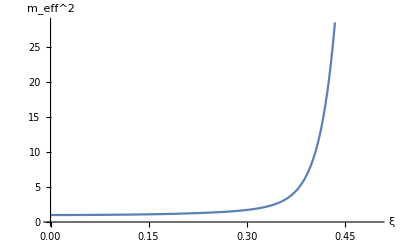

```mathematica
Plot[2(1/2+2 r^2+10 r^4+(172 r^6)/3+358 r^8+(11828 r^10)/5+(732052 r^12)/45+(36296408 r^14)/315+(52601210 r^16)/63+(498972308 r^18)/81+(217917971708 r^20)/4725+(672810390936 r^22)/1925),{r,0,0.5},AxesLabel-> {"ξ","m_eff^2"}]
```

Now fix ξ=0.3 and observe it’s progression with adding more

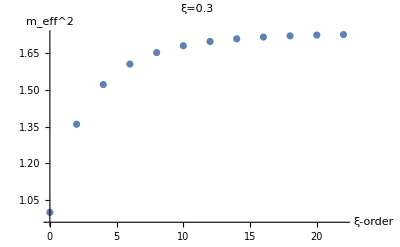

```mathematica
ListPlot[Table[{i,Series[2(1/2+2 r^2+10 r^4+(172 r^6)/3+358 r^8+(11828 r^10)/5+(732052 r^12)/45+(36296408 r^14)/315+(52601210 r^16)/63+(498972308 r^18)/81+(217917971708 r^20)/4725+(672810390936 r^22)/1925),{r,0,i}]//Normal},{i,0,22,2}]/.{r->0.3},AxesLabel-> {"ξ-order","m_eff^2"},PlotLabel->"ξ=0.3",PlotRange->All]
```

### 10. Covariant Potential (Paper version - After Obstruction)

The covariant potential is:

```mathematica
V=-ϕ^2/2+(-1/3+r^2-(3 r^4)/2+(3 r^6)/2-(9 r^8)/8) ϕ^3+( r^2-(19 r^4)/3+(178 r^6)/9-(653 r^8)/18) ϕ^4+(-(16 r^4)/3+(472 r^6)/9-(4307 r^8)/18) ϕ^5+((112 r^6)/3-(7247 r^8)/15 ) ϕ^6-((13451 r^8)/45) ϕ^7;
```

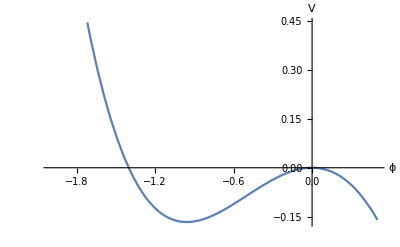

```mathematica
Pot[ϕ_,r_]:=V//Evaluate
Plot[Pot[ϕ,0.2],{ϕ,-2,0.5},AxesLabel->{"ϕ","V"}]
```

Let us find minimum:

```mathematica
ClearAll[B,ϕA,coeff]
ϕA=Sum[B[i]r^i,{i,0,8,2}];
coeff=CoefficientList[Series[D[Pot[ϕ,r],ϕ]/.{ϕ->ϕA},{r,0,8}]//Normal,r];
For[i=0,i≤8,i=i+2,
Set@@@(Solve[coeff[[i+1]]==0,B[i]]//First);
]
ϕA
Series[D[Pot[ϕ,r],ϕ]/.{ϕ->ϕA},{r,0,9}]
```

-1+r^2+(5 r^4)/6+(43 r^6)/18+(2293 r^8)/360

O[r]^10

The depth doesn’t change as:

```mathematica
Series[Pot[ϕA,r],{r,0,9}]//FullSimplify
```

-1/6+O[r]^10

### 11. Covariant Potential (Paper version - Before Obstruction)

The covariant potential is (r^8 \phi^3 coeff is - 129/8 vs -27/4):

```mathematica
V=-ϕ^2/2+(-1/3+r^2-(3 r^4)/2+(3 r^6)/2-(9 r^8)/8) ϕ^3+( r^2-(19 r^4)/3+(178 r^6)/9-(223 r^8)/6) ϕ^4+(-(16 r^4)/3+(472 r^6)/9-(483 r^8)/2) ϕ^5+((112 r^6)/3-485 r^8  ) ϕ^6-((2695 r^8)/9) ϕ^7;
```

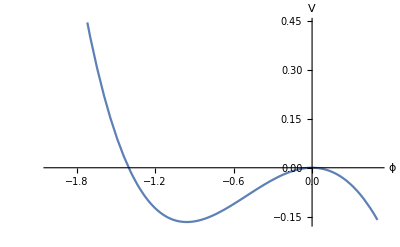

```mathematica
Pot[ϕ_,r_]:=V//Evaluate
Plot[Pot[ϕ,0.2],{ϕ,-2,0.5},AxesLabel->{"ϕ","V"}]
```

Let us find minimum:

```mathematica
ClearAll[B,ϕA,coeff]
ϕA=Sum[B[i]r^i,{i,0,8,2}];
coeff=CoefficientList[Series[D[Pot[ϕ,r],ϕ]/.{ϕ->ϕA},{r,0,8}]//Normal,r];
For[i=0,i≤8,i=i+2,
Set@@@(Solve[coeff[[i+1]]==0,B[i]]//First);
]
ϕA
Series[D[Pot[ϕ,r],ϕ]/.{ϕ->ϕA},{r,0,9}]
```

-1+r^2+(5 r^4)/6+(43 r^6)/18+(155 r^8)/24

O[r]^10

The depth doesn’t change as:

```mathematica
Series[Pot[ϕA,r],{r,0,9}]//FullSimplify
```

-1/6+O[r]^10